## Precision, Accuracy and Machine Precision.

## Machine Precision basics.

Computers have processors. Processors are very complicated and very specialized machines: they are optimized to do some relatively small amount of commands really, really fast. 10^9 operations every second  is somewhat beyond imagination of an ordinary human being.
Every modern processor can work with floats - floating point numbers. If there’re 64 bits to represent the number, then 1 bit represents sign, 11 bits - exponent, the rest 52 bits - fraction. For more on the topic, look at https://en.wikipedia.org/wiki/Double-precision_floating-point_format.
That is one way to compute things with floats - make them 64-bit and use your processor. Another way is to make them any size you want, but use processor to do operations with integer numbers (like fraction and exponent) in algorithms you wrote. That’s usually called “long arithmetic”. The approach is slower - any operation on numbers takes many processor operations, but it can work with numbers that are big enough or precise enough for usual 64-bit arithmetic to give in.

```mathematica
$MachinePrecision
```

15.9546

That’s how many digits you can represent with 64-bit arithmetic. It’s fraction, but

```mathematica
$MachinePrecision Log[10]/Log[2]
```

53.

is exact and is equal to number of bits in the representation of fraction.
Obviously, you cannot add very big number to very small and expect system to remember it. To add float numbers manually, you should first make their exponents equal to the bigger exponent, and then add fractions. So (binary representation!)
1.10101*2^5+1.1*2^2 = 2^5*(1.10101+0.0011)=1.11*2^5
Imagine we can remember only 4 digits after dot. Then exactly
1.1*2^6 + 1 = 2^6*(1.1 + 0.000001)=1.100001*2^6
But with 4-digit precision 1.10001 is equal to 1.1. So no one will ever know that the addition happened. 
Actually, processor rounds numbers which he needs to make “less precise”. Say, 1.100011 with 4-digit precision equals to 1.1001.
Let’s return to machine precision.
The smallest number you can add to 1 and expect a different result is

```mathematica
$MachineEpsilon
```

2.22045×10^-16

```mathematica
1+$MachineEpsilon//InputForm
```

1.0000000000000002

Try any smaller, and

```mathematica
1+$MachineEpsilon/2 -1==0
```

True

Symbols, like π, and numbers without point have infinite precision. We can ask Mathematica directly about that:

```mathematica
{Precision[π],Precision[5/6],Precision[5.5]}
```

{∞,∞,MachinePrecision}

In calculations infinite precision numbers are calculated to a finite precision - by default, to MachinePrecision.

```mathematica
Precision[N[π]]
```

MachinePrecision

If we want more precision, we can use

```mathematica
{N[π,30],Precision[N[π,30]]}
```

{3.14159265358979323846264338328,30.}

There’s function that show the digits of the given number. Let’s ask it to show more digits than the precision we defined.

```mathematica
RealDigits[N[π,5],10,10]
```

{{3,1,4,1,6,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},1}

The second number is just the base of the digits, the third - number of digits I want to see. Last five are Indeterminate - meaning, Mathematica doesn’t know them, but she knows that she doesn’t know. (Is it the first time I called Mathematica “she” in written lectures? “Mathematica” sounds exactly like the word of female gender in Russian, so in my world it’s “she”. You’ll get used to it.))

Precision is important in calculations. Let’s take Taylor series for Sin and plot the result

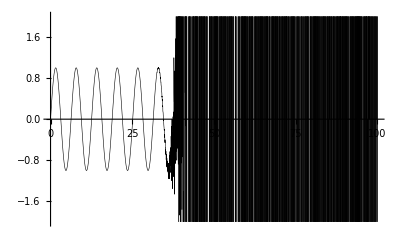

```mathematica
poly[x_]=Normal[Series[Sin[x],{x,0,200}]];
Plot[poly[x],{x,0,100},PlotRange->{-2,2},PlotStyle->{Thickness[0.0010],Black}]
```

One could think that it’s usual divergence of partial series for a function... But it is equal to 0 way too many times for a polynomial of 200th degree. Let’s increase precision.

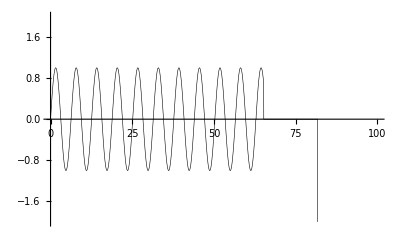

```mathematica
Plot[poly,{x,0,100},PlotRange->{-2,2},PlotStyle->{Thickness[0.0010],Black},WorkingPrecision->30]
```

That’s better, but polynomials don’t usually equal to any number on the whole interval. Let’s increase precision more.

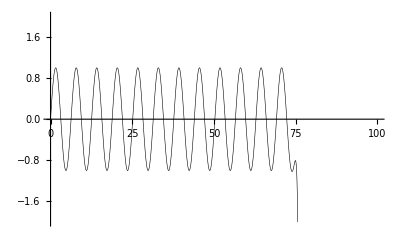

```mathematica
Plot[poly,{x,0,100},PlotRange->{-2,2},PlotStyle->{Thickness[0.0010],Black},WorkingPrecision->60]
```

Ok, that does look like typical series divergence. We can ensure this by increasing precision a little more.

```mathematica
Plot[poly,{x,0,100},PlotRange->{-2,2},PlotStyle->{Thickness[0.0010],Black},WorkingPrecision->80]
```

-Graphics-

Yeah, precision is OK.

### Loss of precision

Precision can be lost. The exact definition of precision is

```mathematica
Precision[x] = -Log10[ϵ/x]
```

where ϵ is the error of x. Meaning, if x has 53 known bits, then 54th is unknown, and its magnitude is approximately the error of x.
Applying function to a number, we are changing precision.

```mathematica
Precision[Exp[N[π,7]]]
```

6.50285

By the way, a little bit easier way to set precision is

```mathematica
5.5`7
```

5.5

I did some trivial computations with the definition of precision and Taylor series and got the following approximate relation:

```mathematica
Precision[f[x]] = Precision[x] - Log10[(x f'[x])/f[x]]
```

It’s almost surely not the way Mathematica computes Precision changes, but it’s more than enough qualitatively. Bigger x, bigger derivative at x, less f[x] - and you are losing Precision. The other way around? You’ll get more precision. That will, basically, mean that error becomes less significant. Like in

```mathematica
Precision[Cos[N[π,5]]]
```

9.30673

Cos(π + ϵ) will have error about ϵ^2, hence, the error becomes much less important.

Another important topic is the way Mathematica treats MachinePrecision. Let’s consider

```mathematica
{Precision[5.5], Precision[Exp[5.5]]}
```

{MachinePrecision,MachinePrecision}

According to all that was written above, we should’ve got 5.5 with MachinePrecision and Exp[5.5] with less than MachinePrecision. And we actually have; what Mathematica means by the second MachinePrecision is “I didn’t calculated, it would be relatively time-consuming”. From the docs (http://reference.wolfram.com/language/tutorial/MachinePrecisionNumbers.html):

The fact that you can get spurious digits in machine-precision numerical calculations with the Wolfram Language is in many respects quite unsatisfactory. The ultimate reason, however, that the Wolfram Language uses fixed precision for these calculations is a matter of computational efficiency.

Nothing to be done here. Just be wary with MachinePrecision: when

```mathematica
{Precision[5`7],Precision[5.5],Precision[5`7 5.5]}
```

{7.,MachinePrecision,MachinePrecision}

7 is actually much smaller than MachinePrecision. In that case, again, “MachinePrecision” means “I don’t know”. The exact same thing with precisions bigger than MachinePrecision:

```mathematica
{Precision[5`20],Precision[5.5],Precision[5`20 5.5]}
```

{20.,MachinePrecision,MachinePrecision}

So, if you want to know the precision of your computation, don’t let any Machine Precision numbers appear in it: only infinite precision ones and with precision manually defined.

Luckily, in most applications you won’t need to think about Precision. But if something strange happens in numerical computations, consider increasing WorkingPrecision or start worrying about the precision of your result. For example, with poly function from above, let’s manually define precision slightly above MachinePrecision and ask for Precision of the computation at some point.

```mathematica
Precision[poly[N[50,16]]]
```

0.

Exactly. With “just” 16 digits of function argument you can’t say anything about poly value at 50. With MachinePrecision?

```mathematica
Precision[poly[50.]]
```

MachinePrecision

The result is as inexact as possible, but since no one cared during the computations, we don’t know that.

## One more thing about discretization.

Let’s consider the integral from the homework.

```mathematica
∫_0^10 1/Cosh[(x-q)^2] ⅆx
```

It is asked to numerically find point of maximum. On the lesson we understood that the analytical solution is really not obvious if one doesn’t do theoretical physics for a living.)) Since it’s not a point of exercise, I’ll just give the answer here: q = 5 is the exact point of maximum.

Trying to compute it as is,

```mathematica
NMaximize[∫_0^10 1/Cosh[(x-q)^2] ⅆx,q]
```

NMaximize::nnum: The function value -∫_0^10 Sech[(0.829053+x)^2]ⅆx is not a number at {q} = {-0.829053}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMaximize[∫_0^10 Sech[(-q+x)^2]ⅆx,q]

We’ll get very long computation and couple of errors. When you’ll understand how to remove those errors (hints are in David’s part), you’ll get some answer. We know MachinePrecision, something about 15.94, we know the analytical answer 5, and it won’t look like first 7 or 8 digits of it are the same as in numerical “answer”. The reason is that there’s an interval of q such that the integral, computed with usual precision, will take one value. The changes of functions are always discretized, since everything is discretized in numerical computations; but for that discretization to be noticed, the first derivative on the interval should be of MachineEpsilon order of magnitude. On the whole interval. Needless to say, it’s very small for relatively big interval of the argument. But magic touch of an exponent can create such an example.

```mathematica
NIntegrate[1/Cosh[(x-5.)^2],{x,0,10}]==NIntegrate[1/Cosh[(x-5.001)^2],{x,0,10}]
```

True

Mathematica just cannot know the true point of maximum with such computations (with MachinePrecision): for every x in, approximately, (4.999; 5.001) the function value is the same and it’s a maximum of all values. The only answer Mathematica can give you is some number from that interval. If you need more precision... Well, use more precise calculations, as was shown in the beginning of the lecture.